1. Rešite naslednje naloge (vsaka od njih je vredna 6 točk):
(a) Poiščite število (576 3001). 3001 je odzgoraj
(b) S funkcijo D izračunajte odvod funkcije sin(3x)+x2−5.
(c) Izračunajte limito zaporedja

an=(1+2n1)n,
ko n→∞.

2. Rešite naslednje naloge (vsaka od njih je vredna 4 točke):
(a) Definirajte funkcijo

r(x,a)=x3+4x−5 deljeno x3 + a
(b) Poiščite realni pol funkcije r(x,4). Pomagajte si lahko s funkcijo Denominator. Pri iskanju ničel lahko uporabite dodaten parameter Reals, da dobite samo realne ničle. Shranite ga v spremenljivko pol.
(c) Narišite graf funkcije r(x,4) na intervalu [−4,4].

```mathematica
Binomial[3001,576]

D[Sin[3 x]+x^2-5,x]

Limit[(1+1/(2 n))^n,n->Infinity]

r[x_,a_]:=(x^3+4 x-5)/(x^3+a)

pol=Solve[Denominator[r[x,4]]==0,x,Reals] (*Denominator vrne imenovalec ulomka, ker iščemo pole, asimptote itd*)

Plot[r[x,4],{x,-4,4}]
```

Definirajte funkciji f(x)=x^2-x in g(x)=(4-x)/(x^2-6x+9).
2. Izračunajte vrednost x, pri kateri funkcija f doseže minimum.
3. Na eno sliko narišite grafa funkcij na intervalu [-2,2].
4. Numerično izračunajte vrednosti x, pri katerih se grafa funkcij f in g na intervalu [-2,2] sekata.
Izračunajte še y koordinate presečišč..

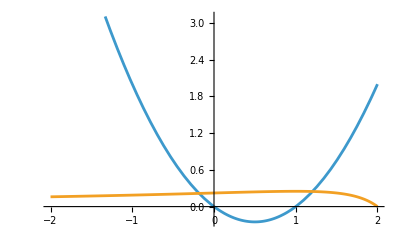

{{x→-0.182271},{x→1.2048}}

{{x→1/2}}

```mathematica
f[x_]:=x^2-x
g[x_]:=(4-x)/(x^2-6x+9)
Plot[{f[x],g[x]},{x,-2,2}] (*Nariše graf funkcije. Potrebuje funkcijo + interval*)
NSolve[f[x]==g[x],x,Reals] (*Reši numerično oz približno.*)
Solve[f'[x]==0] (*Solve izračuna točne oz simbolne rešitve*)
```

Izračunajte limito lim_(z→1+i) (z^4.-1)/(z^2-1)
3.Poiščite vsa taka cela števila m in n, da bo veljalo 42 m+2025 n==3. 
Iskanje rešitev v celih številih lahko določite z dodatnim parametrom Integers.

```mathematica
Limit[(z^4-1)/(z^2-1),z->1+I]
Integrate[x^2Sin[x],{x,0,Pi}]
Solve[42*m+2019*n==3,{m,n},Integers] (*Integers so cela števila, Naravna so NaturalNumbers, racionalna so Rationals, realna so Reals, kompleksna so Complexes*)
```

1+2 ⅈ

-4+π^2

{{m→ConditionalExpression[625+673 C[1], C[1]∈ℤ],n→ConditionalExpression[-13-14 C[1], C[1]∈ℤ]}}

1.  Koliko realnih rešitev ima sistem enačb  x^2 y + y^2 x = 1  in  x^2 + y^2 = 3
2. Izračunajte vrednost izraza 1/(1·2)+1/(2·3)+1/(3·4)+…+1/(2024·2025)
3. Za katera realna števila x velja  Abs[x-2]≤3 x+7 



Izračunajte prvi odvod funkcije ln(sin(e^(2x))) in ga poenostavite.
Numerično izračunajte ničlo funkcije  (cos(x))/(e^(x^3-1)) z začetnim približkom x = 1 .

```mathematica
Length @ Solve[{x^2 y + y^2 x ==1, x^2 + y^2 ==3}, {x, y}, Reals] (*Dobiš en odgovor*)
Sum[1/(k (k + 1)), {k, 1, 2024}]
Reduce[Abs[x - 2] <=3 x + 7, x, Reals]

D[Log[Sin[Exp[2 x]]],x] (*Ali pa [E^(2 x)]*)
FindRoot[Cos[x]/(Exp[x^3-1]),{x,1}] (*iskanje ničel*)
```

4

2024/2025

x≥-5/4

2 ⅇ^(2 x) Cot[ⅇ^(2 x)]

{x→1.5708}

Naj bo dana funkcija f(n)=1/(9 n^2+15 n+4).
1. Definirajte funkcijo f  in izračunajte f(2025).
2. S pomočjo funkcije DiscretePlot narišite točkovni graf f(n) za naravna števila 1≤n≤50.
3. Definirajte funkcijo g kot vsoto g(m) = f(m)+f(m+1)+…+f(2025m).
4. Izračunajte limito lim_(m→∞) g(m).

1/36936004

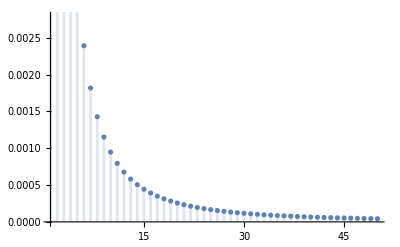

```mathematica
f[n_]:=1/(9n^2+15n+4)
f[2025]

DiscretePlot[f[n],{n,1,50}] (*Nariše vrednosti funkcije samo v diskretnih točkah, ne zvezno krivuljo*)
g[m_]:=Sum[f[i],{i,m,2025m}]
Limit[g[m],m->Infinity];
```

```mathematica
D[X^2 Y + Y^3, X]
```

2 X Y

1. Definirajte funkciji f(x)=x^2+x in g(x)=(2-x)/(x^2-6x+9) ter na eni sliki narišite njuna grafa na intervalu [-2,2].
2. Grafa funkcij f in g se sekata v dveh točkah. Numerično izračunajte x koordinate obeh presečišč.
3. Izračunajte ploščino lika, ki ga omejujeta grafa funkcij f in g.

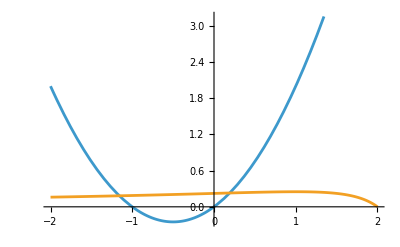

{{x→2.98273-0.292172 ⅈ},{x→2.98273+0.292172 ⅈ},{x→-1.15777},{x→0.192324}}

∫_(2.98273-0.292172 ⅈ)^(2.98273+0.292172 ⅈ) Abs[x+x^2-(2-x)/(9-6 x+x^2)]ⅆx

```mathematica
f[x_]:=x^2 + x
g[x_]:=(2 - x)/(x^2 - 6 x + 9)
Plot[{f[x], g[x]}, {x, -2, 2}]
NSolve[f[x] == g[x], x]

sol = x/. NSolve[f[x] == g[x], x];
Integrate[Abs[f[x]- g[x]], {x, sol[[1]], sol[[2]]}]
```

1. Izračunajte prvi odvod funkcije  2sin (2x+1)  cos (x).
2. Izračunajte vsoto  ∑_(k=1)^∞ (k^2+1)/k^4.
3. Izračunajte limito zaporedja .

```mathematica
D[2 Sin[2 x + 1] Cos[x], x]
Sum[(k^2 + 1)/(k^4), {k, 1, Infinity}]
Limit[Tan[x]/x, x -> 0]
```

4 Cos[x] Cos[1+2 x]-2 Sin[x] Sin[1+2 x]

1/90 π^2 (15+π^2)

1

1. Definirajte funkciji x(t)=cos(3 t) in y(t)=2 sin(t).
2. Narišite parametrično podano krivuljo na območju t ∈[0,2π]. Namig: uporabite lahko funkcijo ParametricPlot.
3. S pomočjo funkcije Solve poiščite take vrednosti t ∈ [0, 2π], da velja x(t)=0. Namig: za dodajanje pogojev lahko uporabite && (“in”).

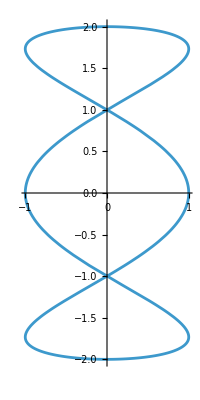

{{t→π/6},{t→π/2},{t→(5 π)/6},{t→(7 π)/6},{t→(3 π)/2},{t→(11 π)/6}}

```mathematica
x[x_]:=Cos[3 t]
y[t_]:=2 Sin[t]
ParametricPlot[{x[t], y[t]}, {t, 0, 2 Pi}] (*Parametrični graf, x in y nista neposredno povezana*)
Solve[Cos[3 t]==0 && 0<=t<=2 Pi, t]
```

1. Izračunajte vrsto .
 2. Izračunajte integral

```mathematica
Sum[1/n^2, {n, 1, Infinity}]
Integrate[Sqrt[x/(1 - x)], {x, 0, 1}]
```

1. (5 točk) Definirajte funkcijo  f, ki sprejme parametra x in y in ima predpis .
2. (5 točk) Narišite graf implicitno podane funkcije, ko je   za  in  . Uporabite funkcijo   ContourPlot.

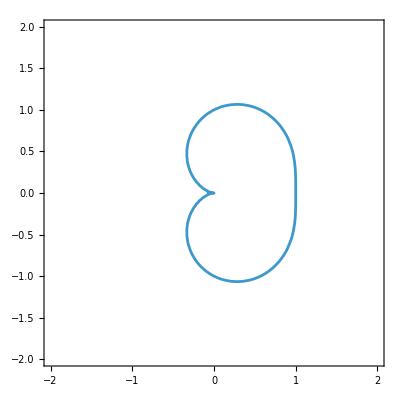

```mathematica
f[x_, y_]:=(x^2 + y^2)^2 - y^2 - x (x^2 + y^2)
ContourPlot[f[x,y]==0, {x, -2, 2}, {y, -2, 2}]
```

1. V spremenljivko potence shranite vse lihe potence števila 2 od 1 do 25, od katerih odštejete 1: 1, 7, 31, 127 ... Pomagajte si z ukazom Table.
2. Izberite vsa števila iz seznama potenc, ki so praštevila. Pomagajte si z ukazom Select.

```mathematica
potence = Table[2^(2 k - 1) - 1, {k, 1, 13}] (*Table ustvari seznam*)
Select[potence, PrimeQ] (*Primeq preveri, če je praštevilo*)
```